```mathematica
Clear["Global`*"];
Needs["VectorAnalysis`"];

G[v_,{p_,λ_,μ_}]:=μ*Exp[λ*(Dot[Normalize[v],Normalize[p]]-1)];
GVec[{x_,y_,z_},{p_,λ_,μ_}]:=G[{x,y,z},{p,λ,μ}];
Print[">SG:"  TraditionalForm[G[v,{p,λ,μ}]]];
```

>SG: (μ ⅇ^(λ (v.p-1)))

```mathematica
GGX[m_,θ_]:=m^2/(π*((Cos[θ]^2*(m^2-1))+1)^2);
Print[">GGX NDF:"];
GGX[m,θ]
```

>GGX NDF:

m^2/(π (1+(-1+m^2) Cos[θ]^2)^2)

```mathematica
DefaultNormalDir={0,0,1};
DefaultLightDir=Normalize[{-1,0,1}];
GGXNDF[m_,viewDir_]:=Module[{H,NoH},
H=Normalize[(DefaultLightDir+viewDir)/2];
NoH=Dot[DefaultNormalDir,H];
GGX[m,NoH]];
GGXSphere[roughness_,θ_,ϕ_]:=Module[{viewDir,halfDir},
viewDir=FromPolarCoordinates[{1,θ,ϕ}];
halfDir=Normalize[(DefaultLightDir+viewDir)/2];
viewDir*GGXNDF[roughness,viewDir]];

Print[">Trying plot 3D GGX lobe:"]
(*ParametricPlot3D[GGXSphere[0.1,θ,ϕ],{θ,0,π},{ϕ,0,2π}];*)
```

>Trying plot 3D GGX lobe:

```mathematica
(*https://computergraphics.stackexchange.com/questions/5955/where-does-the-cosine-factor-comes-from-in-the-ggx-pdf*)
GGX0[m_,θ_]:=m^2/(π*Cos[θ]^4*(m^2+Tan[θ]^2)^2);
ggxIntegral=NIntegrate[GGX0[0.1,θ]*Cos[θ],{θ,-π/2,π/2}];
Print[">Incorrect NDF Integration" ggxIntegral];
```

5.02305 >Incorrect NDF Integration

```mathematica
Manipulate[Plot[{GGX[m,θ]},{θ,-π/2,π/2},PlotRange->Full],{m,0.01,1}]
```

```mathematica
m0=0.2;
(*All Frequency...Eq12*)
ApproxGGX[m_,θ_]:=(1/(π(m^2)))Exp[(2/m^2)*(Cos[θ]-1)];
Print[">Approximate GGX:"];
ApproxGGX[m,θ]
Manipulate[Quiet@Plot[{GGX[m,θ], ApproxGGX[m,θ]},{θ,-π/2,π/2},PlotRange->Full],{m,0.01,1}]
```

>Approximate GGX:

(ⅇ^((2 (-1+Cos[θ]))/m^2))/(m^2 π)

```mathematica
Manipulate[Plot[Abs[GGX[m,θ]- ApproxGGX[m,θ]],{θ,-π/2,π/2},PlotRange->Full],{m,0.01,1}];
p1=Quiet@Plot3D[{GGX[m,θ]},{m,0,1},{θ,-π/2,π/2}];
p2=Quiet@Plot3D[{ApproxGGX[m,θ]},{m,0,1},{θ,-π/2,π/2}];
p3=Quiet@Plot3D[{Abs[GGX[m,θ]-ApproxGGX[m,θ]]},{m,0,1},{θ,-π/2,π/2}];
Print[">NDF Fit Errors:"]
GraphicsRow[{p1,p2,p3}]
```

>NDF Fit Errors:

-Graphics-

```mathematica
ApproxNew1[m_,θ_,a_,b_,c_]:=(a/(m^2))Exp[(b/m^2)*Cos[θ]-c];
Quiet@FindMinimum[NIntegrate[Abs[GGX[0.5,θ]-ApproxNew1[0.5,θ,a,b,c]],{m,0,1},{θ,-π/2,π/2}],{a,1/π},{b,2},{c,1}]
```

{0.198379,{a→0.000776247,b→1.77286,c→1.15421}}

```mathematica
ApproxNew2[m_,θ_]:=(0.0007762473686690445/(m^2))Exp[(1.7728623839792212/m^2)*Cos[θ]-1.1542091163288497];
q1=Plot3D[{GGX[m,θ]},{m,0,1},{θ,-π/2,π/2}];
q2=Plot3D[{ApproxNew2[m,θ]},{m,0,1},{θ,-π/2,π/2}];
q3=Plot3D[{Abs[GGX[m,θ]-ApproxNew2[m,θ]]},{m,0,1},{θ,-π/2,π/2}];
Print[">NDF Fit Errors(2nd):"]
GraphicsRow[{p1,p2,p3}]
```

>NDF Fit Errors(2nd):

-Graphics-

```mathematica
VisSmithG[m_,x_]:=x+Sqrt[m^2+(1-m^2)*x^2];
VisSmith[m_,NoL_,NoV_]:=1/(VisSmithG[m,NoL]*VisSmithG[m,NoV]);
Print[">Vis Smith:   D*G*F/(4*NoL*NoV)=D*Vis*F"];
Manipulate[Plot3D[VisSmith[m,NoL,NoV],{NoL,0,1},{NoV,0,1},PlotRange->Full],{m,0,1}]
```

>Vis Smith:   D*G*F/(4*NoL*NoV)=D*Vis*F

```mathematica
VisSmithApproxG[m_,x1_,x2_]:=x1*(x2*(1-m)+m);
VisSmithApprox[m_,NoL_,NoV_]:=0.5/(VisSmithApproxG[m,NoL,NoV]+VisSmithApproxG[m,NoV,NoL]);
Print[">Vis Smith Approximation:   D*G*F/(4*NoL*NoV)=D*Vis*F"];
Manipulate[Plot3D[VisSmithApprox[m,NoL,NoV],{NoL,0,1},{NoV,0,1},PlotRange->Full],{m,0,1}]
```

>Vis Smith Approximation:   D*G*F/(4*NoL*NoV)=D*Vis*F

```mathematica
VisSmithApproxErrors[m_,NoL_,NoV_]:=Abs[VisSmithApprox[m,NoL,NoV]-VisSmith[m,NoL,NoV]];
Print[">Errors of Vis Smith Approximation:   D*G*F/(4*NoL*NoV)=D*Vis*F"];
Manipulate[Plot3D[VisSmithApproxErrors[m,NoL,NoV],{NoL,0,1},{NoV,0,1},PlotRange->Full],{m,0,1}]
```

>Errors of Vis Smith Approximation:   D*G*F/(4*NoL*NoV)=D*Vis*F

>Origin Fresnel:

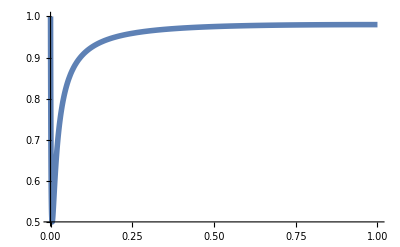

```mathematica
FresnelOriginN[SpecularColor_]:=(1+Sqrt[Max[SpecularColor,0.99]])/(1-Max[SpecularColor,0.99]);
FresnelOriginG[VoH_,SpecularColor_]:=Sqrt[FresnelOriginN[SpecularColor]^2+VoH^2-1];
FresnelOrigin[VoH_,SpecularColor_]:=0.5*((FresnelOriginG[VoH,SpecularColor]-VoH)/(FresnelOriginG[VoH,SpecularColor]+VoH))^2*(1+(((FresnelOriginG[VoH,SpecularColor]+VoH)*VoH-1)/((FresnelOriginG[VoH,SpecularColor]-VoH)*VoH+1))^2);
Print[">Origin Fresnel:"];
Plot[{FresnelOrigin[VoH,0.99]},{VoH,0,1},PlotRange->Full,PlotStyle->{Thickness[0.01]}]
```

>Approximate Fresnel:

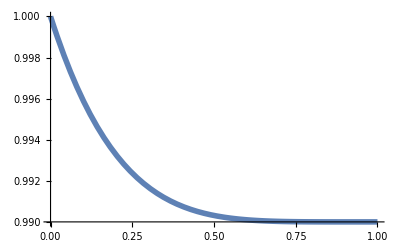

>Approximate Erros:

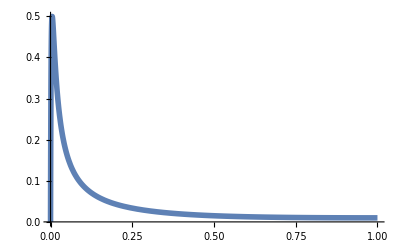

```mathematica
FSchlickFc[VoH_]:=(1-VoH)^5;
FresnelSchlick[VoH_,SpecularColor_]:=Clip[50*SpecularColor,{0,1}]*FSchlickFc[VoH]+(1-FSchlickFc[VoH])*SpecularColor;
Print[">Approximate Fresnel:"];
Plot[{FresnelSchlick[VoH,0.99]},{VoH,0,1},PlotRange->Full,PlotStyle->{Thickness[0.01]}]
Print[">Approximate Erros:"];
Plot[Abs[FresnelOrigin[VoH,0.99]-FresnelSchlick[VoH,0.99]],{VoH,0,1},PlotRange->Full,PlotStyle->Thickness[0.01]]
```